```mathematica
gray=RGBColor[0.7,0.7,0.7];
red=RGBColor[255/255,21/255,21/255];
SetDirectory[NotebookDirectory[]];
```

## A

```mathematica
arrow1=Import["arrows//arrow1.eps"];
arrowleft=Import["arrows//arrowleft.eps"];
arrowright=Import["arrows//arrowright.eps"];
arrow2=Import["arrows//arrow2.eps"];
arrow3=Import["arrows//arrow3.eps"];
arrow4=Import["arrows//arrow4.eps"];
arrow5=Import["arrows//arrow5.eps"];
arrow6=Import["arrows//arrow6.eps"];
arrow7=Import["arrows//arrow7.eps"];
arrow8=Import["arrows//arrow8.eps"];
```

```mathematica
colR=RGBColor[169/255,201/255,205/255];
colF=RGBColor[193/255,58/255,3/255];
colT=RGBColor[8/255,103/255,21/255];
colG=RGBColor[179/255,179/255,179/255];
ρ=0.9;
dYStep={0,-1.4}*ρ;
dXCell={0.62,0}*ρ;
dYCell={0,-0.62}*ρ;
dXSlie={1.2137,0}*ρ;
dYState={0,1.1}*ρ;
radius=0.43/2*ρ;
center={2.5,-1.5}*ρ;
fontSize=8;
fontLegend=6;
color=Black;
xSize=5.4*ρ;
linkWidth=0.0496*ρ;
linkWidth2=0;
linkDistance=0;0.317*ρ;
lineUP[xy_]:=Polygon[{xy+{linkWidth/2,-dYCell[[2]]/2},xy+{linkWidth/2,+dYCell[[2]]/2},xy+{-linkWidth/2,+dYCell[[2]]/2},xy+{-linkWidth/2,-dYCell[[2]]/2}}];
lineWHITE[xy_]:=Polygon[{xy+{linkWidth/2,-dYCell[[2]]/4},xy+{linkWidth/2,+dYCell[[2]]/4},xy+{-linkWidth/2,+dYCell[[2]]/4},xy+{-linkWidth/2,-dYCell[[2]]/4}}];
line3[xy_]:=Polygon[{xy+{dXCell[[1]]+linkDistance+linkWidth2,-linkWidth/2},xy+{dXCell[[1]]+linkDistance,+linkWidth/2},xy+{-dXCell[[1]]-linkDistance-linkWidth2,linkWidth/2},xy+{-dXCell[[1]]-linkDistance,-linkWidth/2}}];
line4[xy_]:=Polygon[{xy+{1.5*dXCell[[1]]+linkDistance+linkWidth2,-linkWidth/2},xy+{1.5*dXCell[[1]]+linkDistance,+linkWidth/2},xy+{-1.5*dXCell[[1]]-linkDistance-linkWidth2,linkWidth/2},xy+{-1.5*dXCell[[1]]-linkDistance,-linkWidth/2}}];
fFamily="Helvetica";
fMain=7;
fLegend=5;
FigA=Graphics[{
(*links*)
Black,
lineUP[center+2*dXCell +3*dYStep+dXSlie    + 1.5*dYCell],
lineUP[center+0*dXCell +3*dYStep-dXSlie    + 1.5*dYCell],
lineUP[center+1*dXCell +3*dYStep-dXSlie    + 1.5*dYCell],
lineUP[center+0*dXCell +2*dYStep-dXSlie    +0.5*dYCell],
line3[center],
line3[center+dYStep],
line3[center+2*dYStep-dXSlie],
line3[center+3*dYStep-dXSlie+dYCell],
line4[center+2*dYStep+dXSlie+0.5*dXCell],
line4[center+3*dYStep+dXSlie+dYCell+0.5*dXCell],

White,
Rotate[lineWHITE[center+1*dXCell +3*dYStep-dXSlie    + 1.5*dYCell],π/4],
Black,
(*states*)
colT,Disk[center-dXCell+dYState,radius],
colF,Disk[center                  +dYState,radius],
colR,Disk[center+dXCell+dYState,radius],

(*row 1*)
colT,Disk[center-dXCell,radius],
colT,Disk[center                  ,radius],
colT,Disk[center+dXCell,radius],

(*row 2*)
colT,Disk[center-dXCell +dYStep,radius],
colF,Disk[center                  +dYStep,radius],
colT,Disk[center+dXCell+dYStep,radius],

(*left column 1*)
colT,Disk[center-dXCell +2*dYStep-dXSlie                 ,radius],
colR,Disk[center                  +2*dYStep-dXSlie                 ,radius],
colR,Disk[center                  +2*dYStep-dXSlie+dYCell,radius],
colF,Disk[center+dXCell+2*dYStep-dXSlie                 ,radius],

(*left column 2*)
colT,Disk[center-dXCell +3*dYStep-dXSlie                 +dYCell,radius],
colR,Disk[center                  +3*dYStep-dXSlie                 +dYCell,radius],
colT,Disk[center                  +3*dYStep-dXSlie+dYCell+dYCell,radius],
colR,Disk[center+dXCell+3*dYStep-dXSlie                 +dYCell,radius],
colR,Disk[center+dXCell+3*dYStep-dXSlie+dYCell+dYCell,radius],

(*right column 1*)
colT,Disk[center-dXCell +2*dYStep+dXSlie                 ,radius],
colR,Disk[center                  +2*dYStep+dXSlie                 ,radius],
colR,Disk[center +dXCell+2*dYStep+dXSlie                 ,radius],
colF,Disk[center+2*dXCell+2*dYStep+dXSlie                 ,radius],

(*right column 2*)
colT,Disk[center-dXCell      +3*dYStep+dXSlie                 +dYCell,radius],
colR,Disk[center                        +3*dYStep+dXSlie                 +dYCell,radius],
colT,Disk[center +dXCell     +3*dYStep+dXSlie                 +dYCell,radius],
colR,Disk[center+2*dXCell+3*dYStep+dXSlie                 +dYCell,radius],
colR,Disk[center+2*dXCell+3*dYStep+dXSlie                 +2*dYCell,radius],

(*NUMBERS*)
Inset[Style["T",FontSize->fontSize,Italic,color,Bold,FontFamily->fFamily],center-dXCell+dYState,{Center,Center}],
Inset[Style["F",FontSize->fontSize,Italic,color,Bold,FontFamily->fFamily],center                  +dYState,{Center,Center}],
Inset[Style["R",FontSize->fontSize,Italic,color,Bold,FontFamily->fFamily],center+dXCell+dYState,{Center,Center}],

(*row 1*)
Inset[Style["1",FontSize->fontSize,color,Bold,FontFamily->fFamily],center-dXCell ,{Center,Center}],
Inset[Style["2",FontSize->fontSize,color,Bold,FontFamily->fFamily],center                   ,{Center,Center}],
Inset[Style["3",FontSize->fontSize,color,Bold,FontFamily->fFamily],center+dXCell ,{Center,Center}],

(*row 2*)
Inset[Style["1",FontSize->fontSize,color,Bold,FontFamily->fFamily],center-dXCell +dYStep,{Center,Center}],
Inset[Style["2",FontSize->fontSize,color,Bold,FontFamily->fFamily],center                   +dYStep,{Center,Center}],
Inset[Style["3",FontSize->fontSize,color,Bold,FontFamily->fFamily],center+dXCell +dYStep,{Center,Center}],

(*left column 1*)
Inset[Style["1",FontSize->fontSize,color,Bold,FontFamily->fFamily],center-dXCell +2*dYStep-dXSlie    ,{Center,Center}],
Inset[Style["2",FontSize->fontSize,color,Bold,FontFamily->fFamily],center                   +2*dYStep-dXSlie    ,{Center,Center}],
Inset[Style["4",FontSize->fontSize,color,Bold,FontFamily->fFamily],center                   +2*dYStep-dXSlie  + dYCell   ,{Center,Center}],
Inset[Style["3",FontSize->fontSize,color,Bold,FontFamily->fFamily],center+dXCell +2*dYStep-dXSlie    ,{Center,Center}],

(*left column 2*)
Inset[Style["1",FontSize->fontSize,color,Bold,FontFamily->fFamily],center-dXCell +3*dYStep-dXSlie    + dYCell,{Center,Center}],
Inset[Style["2",FontSize->fontSize,color,Bold,FontFamily->fFamily],center                   +3*dYStep-dXSlie    + dYCell,{Center,Center}],
Inset[Style["4",FontSize->fontSize,color,Bold,FontFamily->fFamily],center                   +3*dYStep-dXSlie  + dYCell+ dYCell   ,{Center,Center}],
Inset[Style["3",FontSize->fontSize,color,Bold,FontFamily->fFamily],center+dXCell +3*dYStep-dXSlie    + dYCell,{Center,Center}],
Inset[Style["5",FontSize->fontSize,color,Bold,FontFamily->fFamily],center+dXCell +3*dYStep-dXSlie    + dYCell+ dYCell,{Center,Center}],

(*right column 1*)
Inset[Style["1",FontSize->fontSize,color,Bold,FontFamily->fFamily],center-dXCell +2*dYStep+dXSlie                ,{Center,Center}],
Inset[Style["2",FontSize->fontSize,color,Bold,FontFamily->fFamily],center                   +2*dYStep+dXSlie                ,{Center,Center}],
Inset[Style["4",FontSize->fontSize,color,Bold,FontFamily->fFamily],center+dXCell +2*dYStep+dXSlie                ,{Center,Center}],
Inset[Style["3",FontSize->fontSize,color,Bold,FontFamily->fFamily],center+2*dXCell +2*dYStep+dXSlie                ,{Center,Center}],

(*right column 2*)
Inset[Style["1",FontSize->fontSize,color,Bold,FontFamily->fFamily],center-dXCell       +3*dYStep+dXSlie    + dYCell              ,{Center,Center}],
Inset[Style["2",FontSize->fontSize,color,Bold,FontFamily->fFamily],center                         +3*dYStep+dXSlie     + dYCell             ,{Center,Center}],
Inset[Style["4",FontSize->fontSize,color,Bold,FontFamily->fFamily],center+dXCell       +3*dYStep+dXSlie    + dYCell              ,{Center,Center}],
Inset[Style["3",FontSize->fontSize,color,Bold,FontFamily->fFamily],center+2*dXCell +3*dYStep+dXSlie    + dYCell              ,{Center,Center}],
Inset[Style["5",FontSize->fontSize,color,Bold,FontFamily->fFamily],center+2*dXCell +3*dYStep+dXSlie     + dYCell    + dYCell           ,{Center,Center}],

(*ARROWS*)
Inset[arrow1,center                   +0.5*dYStep,{Center,Center}],
Inset[arrow1,center                   +2.5*dYStep+dYCell-dXSlie,{Center,Center}],
Inset[arrow1,center                   +2.5*dYStep+dYCell+dXSlie+0.5*dXCell,{Center,Center}],
Inset[arrowleft,center                   +1.5*dYStep-dXCell,{Center,Center}],
Inset[arrowright,center                   +1.5*dYStep+dXCell,{Center,Center}],

Inset[arrow2,center  +0.5*dXCell-0.5*dYCell,{Center,Center}],
Inset[Subscript[Style["p",Italic,colF,FontSize->fMain,FontFamily->fFamily],Style["i",FontSize->fLegend,FontFamily->fFamily,colF]],center  +0.8*dXCell-1*dYCell,{Left,Center}],

Inset[arrow3,center  +0.5*dXCell-0.5*dYCell+dYStep,{Center,Center}],
Inset[Subscript[Style["p",Italic,colF,FontSize->fMain,FontFamily->fFamily],Style["t",FontSize->fLegend,FontFamily->fFamily,colF]],center  +0.5*dXCell-0.9*dYCell+dYStep,{Center,Center}],

Inset[arrow6,center+1*dXCell +2*dYStep+dXSlie+0.5*dXCell-0.5*dYCell,{Center,Center}],
Inset[
Subscript[Style["p",Italic,colT,FontSize->fMain,FontFamily->fFamily],Style["r",FontSize->fLegend,FontFamily->fFamily,colT]],center+1*dXCell +2*dYStep+dXSlie+0.8*dXCell-1*dYCell,
{Left,Center}],

Inset[arrow7,center+1*dYCell +2*dYStep-dXSlie+0.5*dXCell+0.5*dYCell,{Center,Center}],
Inset[Subscript[Style["p",Italic,colT,FontSize->fMain,FontFamily->fFamily],Style["r",FontSize->fLegend,FontFamily->fFamily,colT]],center+1*dYCell +2*dYStep-dXSlie+0.8*dXCell+0.8*dYCell,{Left,Center}],

Inset[arrow5,center+1*dXCell +3*dYStep-dXSlie    + 1.5*dYCell+0.5*dXCell-0.5*dYCell+0.2*dYCell-0.08*dXCell,{Center,Center}],
Inset[Subscript[Style["p",Italic,colG,FontSize->fMain,FontFamily->fFamily],Style["c",FontSize->fLegend,FontFamily->fFamily,colG]],center+1*dXCell +3*dYStep-dXSlie    + 1.5*dYCell +0.8*dXCell-1*dYCell+0.2*dYCell-0.08*dXCell,{Left,Center}]

}

,PlotRange->{{0,xSize},{-6.5,0}},ImageSize->cm[xSize]]
```

-Graphics-

## B

```mathematica
getColors[str_]:=(
If[str=="Green",col=RGBColor[8/255,103/255,21/255]];
If[str=="Red",col=RGBColor[193/255,58/255,3/255]];
If[str=="Blue",col=RGBColor[169/255,201/255,205/255]];
col)

maxClone[pi_,pt_,pr_,pd_,clone_,time_]:=(
colorsIN=Import["FFM_movie_links//output//graphs//graph_color_pi_"<>ToString[pi]<>"_pt_"<>ToString[pt]<>"_pr_"<>ToString[pr]<>"_pd_"<>ToString[pd]<>"_clone_"<>ToString[clone]<>"_"<>ToString[time]<>".dat"];
colors={};
Do[AppendTo[colors,colorsIN[[ii]][[1]]->{getColors[colorsIN[[ii]][[2]]],EdgeForm[None]}],{ii,1,Length[colorsIN]}];
linksIN=Import["FFM_movie_links//output//graphs//graph_links_pi_"<>ToString[pi]<>"_pt_"<>ToString[pt]<>"_pr_"<>ToString[pr]<>"_pd_"<>ToString[pd]<>"_clone_"<>ToString[clone]<>"_"<>ToString[time]<>".dat"];
links={};
vertices={};
Do[
v1=linksIN[[ii]][[1]];
v2=linksIN[[ii]][[2]];
AppendTo[vertices,v1];
AppendTo[vertices,v2];
If[v1≠v2,AppendTo[links,v1<->v2]];
,{ii,1,Length[linksIN]}];
vertices=DeleteDuplicates[vertices];
Length[ConnectedComponents[links][[1]]])
```

334

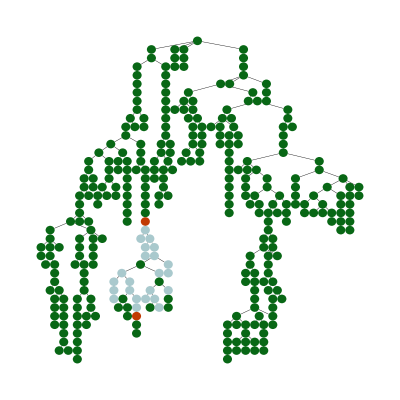

```mathematica
maxClone["0.0001",0.7,"0.158114",0.026,0,1001]
xx=0.018;
sc=0.02;
FigB=Subgraph[links,WeaklyConnectedComponents[links][[1]],AspectRatio->1,ImageSize->cm[6],GraphLayout->"LayeredEmbedding",VertexStyle->colors,EdgeStyle->If[Length[vertices]>10,{{Opacity[1],Black,AbsoluteThickness[cm[0.01]]}},{{Opacity[1],Black,AbsoluteThickness[cm[0.02]]}}],
VertexSize->1,ImageSize->cm[9]]
```

## C

```mathematica
xMin=0.5;
xMax=4.2;
yMin=0;
yMax=0.2;
xMax2=xMax-xMin;
dx=0.1;
dy=0.5;
dy2=0.15;
dy3=0.22;
cfMAX[x_]:=ColorData["SunsetColors"][(x-0.1)/0.45];
barC=Graphics[{
{Raster[{Range[0.1,0.55,1/1000]},{{xMin,yMin},{xMax,yMax}},ColorFunction->cfMAX]},AbsoluteThickness[cm[0.02]],Line[{{xMin,yMin},{xMax,yMin},{xMax,yMax},{xMin,yMax},{xMin,yMin}}],
Line[{{xMin+0/3*xMax2,0},{xMin+0/3*xMax2,-dy2}}],
Line[{{xMin+1/3*xMax2,0},{xMin+1/3*xMax2,-dy2}}],
Line[{{xMin+2/3*xMax2,0},{xMin+2/3*xMax2,-dy2}}],
Line[{{xMin+3/3*xMax2,0},{xMin+3/3*xMax2,-dy2}}],
Line[{{xMin+1*xMax2,0},{xMin+1*xMax2,-dy2}}],
Inset[Style["0.1",FontFamily->"Helvetica",FontSize->7],{xMin+0/3*xMax2,-dy3},{Center,Top}],
Inset[Style["0.25",FontFamily->"Helvetica",FontSize->7],{xMin+1/3*xMax2,-dy3},{Center,Top}],
Inset[Style["0.4",FontFamily->"Helvetica",FontSize->7],{xMin+2/3*xMax2,-dy3},{Center,Top}],
Inset[Style["0.55",FontFamily->"Helvetica",FontSize->7],{xMin+3/3*xMax2,-dy3},{Center,Top}]




},PlotRange->{{0,xMax+xMin},{yMin-2*dy,yMax+dy}},ImageSize->cm[xMax+xMin],ImagePadding->0]
```

-Graphics-

```mathematica
fixNum[num_]:=(
If[StringCount[num,"e"]==1,ToExpression[StringTake[num,{1,-5}]]*10^-5.,ToExpression[num]]
)
fixNumList[numIN_]:=(
numOUT={};Do[AppendTo[numOUT,fixNum[numIN[[ii]]]],{ii,1,Length[numIN]}];numOUT

)
ffmMAX[pi_,pt_,pr_,pd_]:=(
maxIN=Import["FFM//output//max//max_pi_"<>ToString[pi]<>"_pt_"<>ToString[pt]<>"_pr_"<>ToString[pr]<>"_pd_"<>ToString[pd]<>"_.dat","Table"];
max={};Do[AppendTo[max,maxIN[[ii]][[1]]],{ii,1,Length[maxIN]}];
{pt,Log[fixNum[pr]/fixNum[pi]],Mean[max]}
)
minMax[v_,x0_,x1_,y0_,y1_]:=(
{Min[Max[v[[1]],x0],x1],Min[Max[v[[2]],y0],y1]})
piForPlot="0.0001";
ptList={0,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1};
prList={
"1",

"0.88914",
"8.8914e-05",
"0.088914",
"0.0088914",
"0.00088914",

"1.58114e-05",
"0.158114",
"0.0158114",
"0.00158114",
"0.000158114",

"2.81171e-05",
"0.281171",
"0.0281171",
"0.00281171",
"0.000281171",

"5e-05",
"0.5",
"0.05",
"0.005",
"0.0005"
};
maxOutList={};
maxAllList={};

linesExperiment={};

(*x distance between points*)
dx=0.05;

(*y distance between points*)
dy0=Log[Sort[fixNumList[prList]/fixNum[piForPlot]]][[2]]-Log[Sort[fixNumList[prList]/fixNum[piForPlot]]][[1]];
dy1=Log[Sort[fixNumList[prList]/fixNum[piForPlot]]][[-1]]-Log[Sort[fixNumList[prList]/fixNum[piForPlot]]][[-2]];

size=3*6/5;

(*smallest and largest values in x,y direction*)
xMIN=0;
xMAX=1;
yMIN=Log[Sort[fixNumList[prList]/fixNum[piForPlot]]][[1]];
yMAX=Log[Sort[fixNumList[prList]/fixNum[piForPlot]]][[-1]];

Do[
Print[i];
Do[
GG=ffmMAX[piForPlot,ptList[[i]],prList[[j]],0.026];
AppendTo[maxOutList,GG];
AppendTo[maxAllList,GG[[3]]];

If[Abs[GG[[3]]-0.36]<0.06,

x0=GG[[1]];
y0=GG[[2]];

(*if p_r == 1, dy is smaller*)
If[prList[[j]]=="1",dy=dy1,dy=dy0];

(*if p_r == 1, dy is smaller*)
If[prList[[j]]=="0.88914",dyUP=dy1,dyUP=dy0];

(*add four lines surrounding the coordinate if withing standard deviation of experiment*)
AppendTo[linesExperiment,{
minMax[{x0-dx/2,y0-dy/2},xMIN,xMAX,yMIN,yMAX],
minMax[{x0+dx/2,y0-dy/2},xMIN,xMAX,yMIN,yMAX]
}];
AppendTo[linesExperiment,{
minMax[{x0+dx/2,y0-dy/2},xMIN,xMAX,yMIN,yMAX],
minMax[{x0+dx/2,y0+dyUP/2},xMIN,xMAX,yMIN,yMAX]
}];
AppendTo[linesExperiment,{
minMax[{x0-dx/2,y0+dyUP/2},xMIN,xMAX,yMIN,yMAX],
minMax[{x0+dx/2,y0+dyUP/2},xMIN,xMAX,yMIN,yMAX]
}];
AppendTo[linesExperiment,{
minMax[{x0-dx/2,y0-dy/2},xMIN,xMAX,yMIN,yMAX],
minMax[{x0-dx/2,y0+dyUP/2},xMIN,xMAX,yMIN,yMAX]
}];

];

,{j,1,Length[prList]}],{i,1,Length[ptList]}]
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

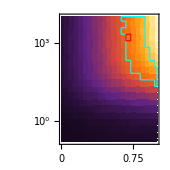

```mathematica
b=ListDensityPlot[maxOutList,ColorFunction->cfMAX,ColorFunctionScaling->False,InterpolationOrder->0,PlotRange->{{0,1},{yMIN,yMAX},{0.1,0.55}}];


(*Lines around experimentally comparable values*)
lineColor=Cyan;
lineTh=0.03;

isSame[v1_,v2_]:=Total[Total[Abs[v1-v2]]]<0.0001
count2[xyz_,x_]:=(
cn=0;Do[If[isSame[xyz[[ii]],x],cn+=1],{ii,1,Length[xyz]}];
cn)
trueLines[linesIN_]:=(
linesOUT={};
Do[
If[count2[linesIN,linesIN[[jj]]]==1,AppendTo[linesOUT,linesIN[[jj]]]],{jj,1,Length[linesIN]}];
linesOUT)
linesplot=ListLinePlot[trueLines[linesExperiment],PlotRange->{
{0,1},{Log[Sort[fixNumList[prList]/fixNum[piForPlot]]][[1]],Log[Sort[fixNumList[prList]/fixNum[piForPlot]]][[-1]]}},PlotStyle->{{lineColor,AbsoluteThickness[cm[lineTh]]}},AspectRatio->1];

(*Lines around best fit*)
linesBestFit={{0.675,Log[0.158114/0.0001]+dy0/2.},
{0.725,Log[0.158114/0.0001]+dy0/2.},
{0.725,Log[0.158114/0.0001]-dy0/2.},
{0.675,Log[0.158114/0.0001]-dy0/2.},{0.675,Log[0.158114/0.0001]+dy0/2.}};
linesplot2=ListLinePlot[linesBestFit,PlotRange->{
{0,1},{Log[Sort[fixNumList[prList]/fixNum[piForPlot]]][[1]],Log[Sort[fixNumList[prList]/fixNum[piForPlot]]][[-1]]}},PlotStyle->{{Red,AbsoluteThickness[cm[lineTh]]}},AspectRatio->1];


fLegend=5;
FigC=plotBack[
{b,linesplot,linesplot2},
xTicks->{0,0.25,0.5,0.75,1},
yTicks->{Log[0.000001],Log[0.00001],Log[0.0001],Log[0.001],Log[0.01],Log[0.1],Log[1],Log[10],Log[100],Log[1000],Log[10000]},
yReplace->{Row[{Superscript[Style["10"],Style["-6",FontSize->fLegend]]}],Row[{Superscript[Style["10"],Style["-5",FontSize->fLegend]]}],Row[{Superscript[Style["10"],Style["-4",FontSize->fLegend]]}],Row[{Superscript[Style["10"],Style["-3",FontSize->fLegend]]}],Row[{Superscript[Style["10"],Style["-2",FontSize->fLegend]]}],Row[{Superscript[Style["10"],Style["-1",FontSize->fLegend]]}],Row[{Superscript[Style["10"],Style["0",FontSize->fLegend]]}],Row[{Superscript[Style["10"],Style["1",FontSize->fLegend]]}],Row[{Superscript[Style["10"],Style["2",FontSize->fLegend]]}],Row[{Superscript[Style["10"],Style["3",FontSize->fLegend]]}],Row[{Superscript[Style["10"],Style["4",FontSize->fLegend]]}]},
tickLength->0.12,
plotRange->{{0,1},{yMIN,yMAX}},
plotDimensions->{3*6/5,3*6/5},
plotMargins->{1.2,0.6,1.2,1.2},
plotLabels->{
Row[{
Style["Coupling "],Subscript[Style["p",Italic],Style["t",FontSize->fLegend]]}],
Row[{Style["Ratio "],Subscript[Style["p",Italic],Style["r",FontSize->fLegend]],Style["/"],Subscript[Style["p",Italic],Style["i",FontSize->fLegend]]}]},
labelsDistance->{0.55,0.8},
plotTitle->True,
titleText->Row[{Style["Forest Fire ("],Subscript[Style["p",Italic],Style["i",FontSize->fLegend]],
Style[" = "],Style[piForPlot],Style[")"]}],
titleDistance->0.25,
fontMain->7,
fontName->"Helvetica"
]
```

## Fig D

```mathematica
getTheoryData[pi_,pt_,pr_,pd_,n_]:=(
a=Import["FFM//output//diversity//diversity_pi_"<>ToString[pi]<>"_pt_"<>ToString[pt]<>"_pr_"<>ToString[pr]<>"_pd_"<>ToString[pd]<>"_.dat","Table"];
out={};
Do[
nnn=a[[i]][[-1]];
If[nnn<2&&i>61,Print["nnn error"<>ToString[i]]];
If[a[[i]][[2]]≠-1&&a[[i]][[1]]>61,AppendTo[out,{{a[[i]][[1]],a[[i]][[2*n]]},ErrorBar[a[[i]][[2*n + 1]]*√(nnn/(nnn-1))]}]],{i,1,1001}];
out
)
BP[n_]:=Max[n]/Total[n]
Gini[x_]:=N[Sum[Sum[Abs[x[[i]]-x[[j]]],{j,1,Length[x]}],{i,1,Length[x]}]/(2*Length[x]*Sum[x[[j]],{j,1,Length[x]}])]
```

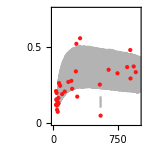

```mathematica
margins={0.9,0.5,1.2,0.4};
distance={0.6,0.6};
sizes={3*6/5,3*6/5};
fractionFig[pi_,pt_,pr_,pd_]:=(
(*theory values*)
b=getTheoryData[pi,pt,pr,pd,8];

(*experimental values*)
fAll={};
f=BP;
Do[
c=Import["chambers/c"<>ToString[j]<>".dat","List"];
AppendTo[fAll,{Total[c],N[f[c]]}]
,{j,1,21}];
Do[
c=Import["chambers/s"<>ToString[j]<>".dat","List"];
AppendTo[fAll,{Total[c],N[f[c]]}]
,{j,1,11}];

(*add legends*)
xLegend=550;
yLegend1=0.14;
yLegend2=yLegend1-0.12*0.75;
yError=0.05*0.75;
AppendTo[b,{{xLegend,yLegend1},ErrorBar[yError]}];
AppendTo[fAll,{xLegend,yLegend2}];

(*plots*)
p1=ErrorListPlot[b,PlotRange->{{0,1000},{0,0.75}},PlotStyle->gray];
p2=ListPlot[fAll,PlotRange->{0,4},PlotStyle->{red,PointSize->Medium}];
p3=Show[{p1,p2},Frame->True,Axes->False];

p4=plot[
{p3(*fit[gam,pMax],*)},
xTicks->{0,250,500,750,1000},
yTicks->{0,0.25,0.5,0.75},
tickLength->0.12,
plotRange->{{0,1000},{0,0.75}},
plotDimensions->sizes,
plotMargins->margins,
plotLabels->{
Row[{Style["Cell number"]}],
Row[{Style["Largest cluster fractional size"]}]},
labelsDistance->{0.5,0.85},
plotTitle->True,
titleText->Row[{Style[""]}],
titleDistance->0.25,
fontMain->7,
fontName->"Helvetica"
]
)
figD=fractionFig["0.0001",0.7,"0.158114",0.026];
t1=Style["Theory",FontSize->6,FontFamily->"Helvetica",gray];
t2=Style["Experiment",FontSize->6,FontFamily->"Helvetica",red];
ddx=0.2;
FigD=figure[6,5,
elements->{figD,t1,t2},
elementCoordinates->{
{0,0},
{1.2+3*6/5*(xLegend/1000)+ddx,-0.5-(0.75-yLegend1)/0.75*3*6/5},
{1.2+3*6/5*(xLegend/1000)+ddx,-0.5-(0.75-yLegend2)/0.75*3*6/5}
},
yCenteredElements->{2,3}]
```

## E

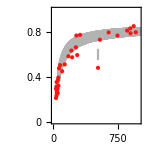

```mathematica
ginniFig[pi_,pt_,pr_,pd_]:=(
(*theory values*)
b=getTheoryData[pi,pt,pr,pd,1];

(*experimental values*)
fAll={};
f=Gini;
Do[
c=Import["chambers//c"<>ToString[j]<>".dat","List"];
AppendTo[fAll,{Total[c],N[f[c]]}]
,{j,1,21}];
Do[
c=Import["chambers//s"<>ToString[j]<>".dat","List"];
AppendTo[fAll,{Total[c],N[f[c]]}]
,{j,1,11}];

(*add legends*)
xLegend=520;
yLegend1=0.6;
yLegend2=0.48;
yError=0.05;
AppendTo[b,{{xLegend,yLegend1},ErrorBar[yError]}];
AppendTo[fAll,{xLegend,yLegend2}];

(*plots*)
p1=ErrorListPlot[b,PlotRange->{{0,1000},{0,1}},PlotStyle->gray];
p2=ListPlot[fAll,PlotRange->{0,1},PlotStyle->{red,PointSize->Medium}];
p3=Show[{p1,p2},Frame->True,Axes->False];
p4=plot[
{p3(*fit[gam,pMax],*)},
xTicks->{0,250,500,750,1000},
yTicks->{0,0.2,0.4,0.6,0.8,1},
tickLength->0.12,
plotRange->{{0,1000},{0,1}},
plotDimensions->sizes,
plotMargins->margins,
plotLabels->{
Row[{Style["Cell number"]}],
Row[{Style["Gini coefficient "],Style["G",Italic]}]},
labelsDistance->{0.55,0.75},
plotTitle->True,
titleText->Row[{Style[""]}],
titleDistance->0.25,
fontMain->7,
fontName->"Helvetica"
]
)
figE=ginniFig["0.0001",0.7,"0.158114",0.026];
t1=Style["Theory",FontSize->6,FontFamily->"Helvetica",gray];
t2=Style["Experiment",FontSize->6,FontFamily->"Helvetica",red];
ddx=0.2;
FigE=figure[6,5,
elements->{figE,t1,t2},
elementCoordinates->{
{0,0},
{1.2+3*6/5*(xLegend/1000)+ddx,-0.5-(1-yLegend1)*3*6/5},
{1.2+3*6/5*(xLegend/1000)+ddx,-0.5-(1-yLegend2)*3*6/5}
},
yCenteredElements->{2,3}]
```

## Figure 3

```mathematica
fName="Helvetica";
t1=Row[{Subscript[Style["p",Italic,FontFamily->fName,FontSize->6],Style["i",FontFamily->fName,FontSize->4]],Style[StringJoin[" = 0.0001"],FontFamily->fName,FontSize->6]}];
t2=Row[{Subscript[Style["p",Italic,FontFamily->fName,FontSize->6],Style["t",FontFamily->fName,FontSize->4]],Style[StringJoin[" = 0.7"],FontFamily->fName,FontSize->6]}];
t3=Row[{Subscript[Style["p",Italic,FontFamily->fName,FontSize->6],Style["r",FontFamily->fName,FontSize->4]],Style[" = 0.1581",FontFamily->fName,FontSize->6]}];
t4=Row[{Subscript[Style["p",Italic,FontFamily->fName,FontSize->6],Style["c",FontFamily->fName,FontSize->4]],Style[StringJoin[" = 0.026"],FontFamily->fName,FontSize->6]}];
center={0.1,0};
dxx={0,-0.29};
l1a=figure[
1.8,
1.4,
elements->{t1,t2,t3,t4},
elementCoordinates->{center,center+1*dxx,center+2*dxx,center+3*dxx}];
tMAX=Row[{Style["Largest cluster fractional size",FontFamily->"Arial",FontSize->7]}];
tFFM=Row[{Style["Forest Fire model:",FontFamily->"Arial",FontSize->7]}];
ddX=0;
ddY=1.5;
dYGH=-8.7;
dYIJK=-13.8;
dXL=0.2;
dX=5.6;
dY=-5;
dYL=0.8;
dYR=1.4;
dY2=-1.2;

ddY2=1;
dyc=0.2;
ddY3=0.5;
Fig3=figure[16.8,12.2,
elements->{
tMAX,
barC,
tFFM,

FigA,
FigB,
FigC,

FigD,
FigE,

l1a,
l1a,
l1a



},
elementCoordinates->{
{2*dX+1.2+3*6/5/2,-0.4-dyc},
{2*dX+1.2+3*6/5/2,-1.1-dyc},
{0.2+2.5*ρ,-0.5},

{0.2,-6.6-dY+ddY2},
{-0.4+dX,-6.5-dY+ddY2},
{2*dX,dY2-0.3-dyc},

{0.5*dX,2*dY+dYR+ddY2+ddY3-0.1},
{1.5*dX,2*dY+dYR+ddY2+ddY3-0.1},

{5.3,-6.7+ddY2+5.2},
{14.2-1.*dX+0.5*dX,-10.5+ddY2-0.6+ddY3},
{14.2-2*dX+0.45+0.5*dX,-10.5+ddY2-0.6+ddY3+1.95}

},
letters->{
Style["a",Bold,FontFamily->"Helvetica",FontSize->8],
Style["b",Bold,FontFamily->"Helvetica",FontSize->8],
Style["c",Bold,FontFamily->"Helvetica",FontSize->8],
Style["d",Bold,FontFamily->"Helvetica",FontSize->8],
Style["e",Bold,FontFamily->"Helvetica",FontSize->8]},
letterCoordinates->{
{0.2,0},
{-0.4+dX,0},
{2*dX,0},

{0.5*dX,2*dY+dYR+ddY2+ddY3-0.1},
{1.5*dX+0.1,2*dY+dYR+ddY2+ddY3-0.1}
},
centeredElements->{1,2,3}]
```

-Graphics-

```mathematica
Export["figs//SYS_Fig3.pdf",Fig3]
```

figs//SYS_Fig3.pdf